```mathematica
x0 = 0; x1 = Pi/6; x2 = Pi/3; x3=Pi/2
y0 = 0; y1 = 1/2; y2 = Sqrt[3]/2; y3=1;
```

```mathematica
(*Lagrange basis polynomials*)
```

```mathematica
l0[x_] = (x-x1)(x-x2)(x-x3)/((x0-x1)(x0-x2)(x0-x3));
l1[x_] = (x-x0)(x-x2)(x-x3)/((x1-x0)(x1-x2)(x1-x3));
l2[x_] = (x-x0)(x-x1)(x-x3)/((x2-x0)(x2-x1)(x2-x3));
l3[x_] = (x-x0)(x-x1)(x-x2)/((x3-x0)(x3-x1)(x3-x2));
```

```mathematica
p[x_] =l0[x]y0 +l1[x]y1+l2[x]y2+l3[x]y3;
```

```mathematica
plot1 = Plot[p[x], {x, 0 , Pi/3}];
```

```mathematica
plot2 = ListPlot[{{x0, y0}, {x1, y1},{x2, y2},{x3, y3}}, PlotStyle->Orange];
```

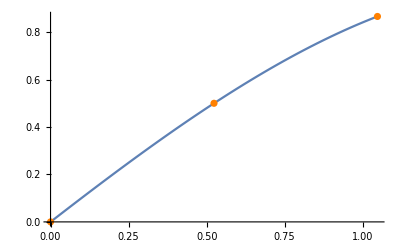

```mathematica
Show[{plot1, plot2}]
```

```mathematica
R[x_] = 1/24(T[x]);
R[Pi/5]//N
```

0.00108232

```mathematica
T[x_] = (x-x0)(x-x1)(x-x2)(x-x3);
R[x_] = 1/24(T[x]);
R[Pi/5]//N
0.0010823232337111382
```

```mathematica
Sin[Pi/5]//N
0.5877852522924731
```

```mathematica
(Sin[Pi/5.]-p[Pi/5.])
0.000723765075034466
```

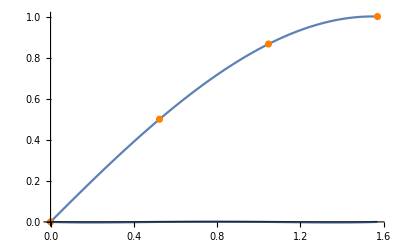

```mathematica
plotR  = Plot[R[x],{x, 0, Pi/2}];
plot2 = ListPlot[{{x0, y0}, {x1, y1},{x2, y2},{x3, y3}}, PlotStyle->Orange];
plot1 = Plot[p[x], {x, 0 , Pi/2}];
Show[{plot1, plot2, plotR}]
```

```mathematica
A[x_] =Sin[x]-p[x];
```

```mathematica
plotA = Plot[Abs[A[x]], {x,0, Pi/2 }];
R[x_] = 1/24(T[x]);
plotR = Plot[Abs[R[x]], {x,0, Pi/2}];
```

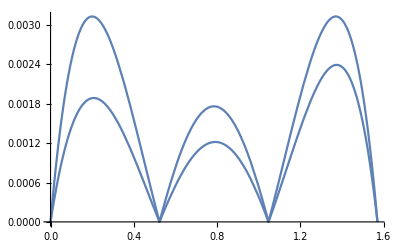

```mathematica
Show[plotA, plotR,PlotRange->All]
```

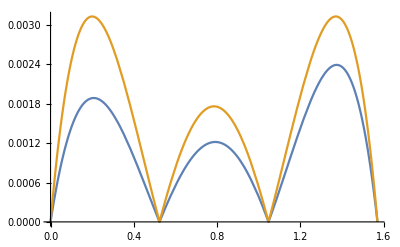

```mathematica
Plot[{Abs[A[x]],Abs[R[x]]}, {x,0, Pi/2}]
```

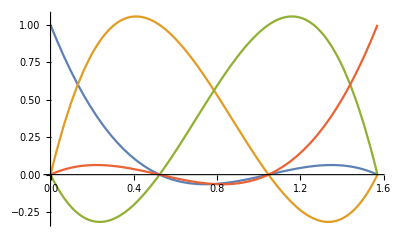

```mathematica
Plot[{l0[x],l1[x], l2[x], l3[x]}, {x,0, Pi/2}]
```

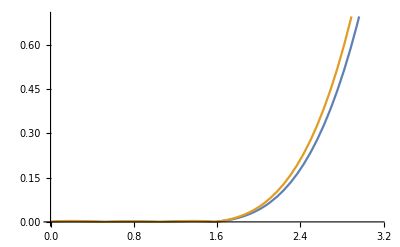

```mathematica
Plot[{Abs[A[x]],Abs[R[x]]}, {x,0, Pi}]
```

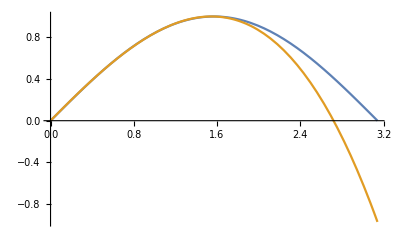

```mathematica
Plot[{Sin[x],p[x]}, {x,0, Pi}]
```

```mathematica
Derivative[1/1+x]
```

Derivative[1+x]

```mathematica
D[1/(x+1), x]
```

-1/(1+x)^2

```mathematica
D[-1/(1+x)^2 , x]
```

2/(1+x)^3